```mathematica
raSinh[x_,h_,H_]:=Evaluate[D[Sinh[x*h]/Sinh[x*H],x]];
a6[x_,h_,H_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*Sinh[x*(H-h)]-(H-h)Sinh[x*h]Sinh[x H])Sinh[x(H-x3)]-
(Sinh[x*H] raSinh[x,h,H]-x*H raSinh[x,H-h,H])*Sinh[x*H]*Cosh[x*(H-x3)]
);
a6bar[x_,h_,H_]:=x^-2*(
(x*h*H*Sinh[x*(H-h)]-(H-h)Sinh[x*h]Sinh[x H])Sinh[x(H-x3)]-
(Sinh[x*H] raSinh[x,h,H]-x*H raSinh[x,H-h,H])*Sinh[x*H]*Cosh[x*(H-x3)]
);

a5[x_,h_,H_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*Sinh[x*(H-h)]+(H-h)Sinh[x*h]Sinh[x H])Cosh[x(H-x3)]+
(Sinh[x*H] raSinh[x,h,H]+x*H raSinh[x,H-h,H])*Sinh[x*H]*Sinh[x*(H-x3)]
)
```

```mathematica
a3[x_,h_,H_]:=(Sinh[x*H]^2)^-1*
(h*Sinh[x*H]Cosh[x(H-x3-h)]-H*Sinh[x*h]Cosh[x(H+x3)]
)
```

```mathematica
a4[x_,h_,H_]:=x/(Sinh[x*H]^2-(x*H)^2)*(
x3 x H(h Sinh[x (x3-h)]
+H Sinh[x h]Sinh[x(H-x3)]/Sinh[x H]
-x h H^2 Sinh[x x3]Sinh[x(H-h)]/Sinh[x H]
+(KroneckerDelta[j,3]-KroneckerDelta[k,3])
*(-H(H-h)Sinh[x h]Sinh[x x3]+x3(h Sinh[x H]Sinh[x(H-x3-h)]+H Sinh[x h]Sinh[x x3])))
);
```

```mathematica
Parallelize[Table[NIntegrate[BesselJ[0,ρ x]a6[x,h,H]/.{h->0.1,H->1,ρ->0.1,x3->0.2},{x,0.01,xmax}]//AbsoluteTiming,{xmax,10,100,5}]]
```

{{0.04103,-3.81854},{0.04003,-5.03487},{0.03803,-5.35771},{0.04503,-5.39107},{0.03803,-5.37641},{0.04103,-5.36609},{0.04303,-5.36225},{0.04003,-5.36121},{0.04603,-5.361},{0.03703,-5.36097},{0.05204,-5.36098},{0.05104,-5.36098},{0.05304,-5.36098},{0.05304,-5.36098},{0.07605,-5.36098},{0.07005,-5.36098},{0.05304,-5.36098},{0.05404,-5.36098},{0.08606,-5.36098}}

```mathematica
AbsoluteTiming@NIntegrate[BesselJ[0,ρ x]a6[x,h,H]/.{h->0.1,H->1,ρ->0.1,x3->0.2},{x,0,0.01}]
```

{0.03102,-3.60003×10^-6}

```mathematica
33
```

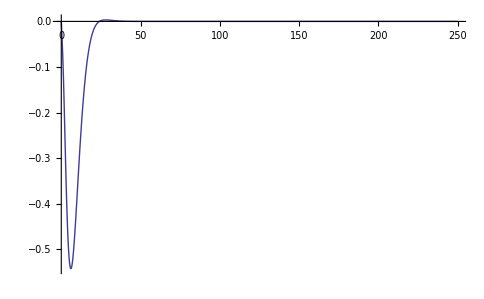

```mathematica
Plot[BesselJ[0,ρ x]a6[x,h,H]/.{h->0.1,H->1,x3->0.2,ρ->0.1},{x,0,250},PlotRange->All]
```

```mathematica
a1[x_,h_,H_]:=1/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*x3*Sinh[x*(H-x3)]Sinh[x(H-h)]+x3(h Sinh[x H]Cosh[x(H-x3-h)])-H Sinh[x*h]Cosh[x3 H])

+x3 x H Sinh[x H]Cosh[x(H-x3)]raSinh[x,H-h,H]
-H Sinh[x x3](Sinh[x*H] raSinh[x,h,H]+x*H raSinh[x,H-h,H])
)

a2[x_,h_,H_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
x3((H Sinh[x*H]Cosh[x x3]-h Sinh[x H]Cosh[x(H-x3-h)]
+x h H Sinh[x*(H-x3)]Sinh[x (H-h)])
+x H Cosh[x(H-x3)]Sinh[x*H] raSinh[x,H-h,H]
-x*H^2 Sinh[x x3] raSinh[x,H-h,H])+H Sinh[x*x3]*Sinh[x*H] raSinh[x,h,H]
)
```

```mathematica
a6[x,h,H]
```

1/(sinh^2(H x)-H^2 x^2)x^2 ((h H x sinh(x (H-h))-(H-h) sinh(h x) sinh(H x)) sinh(x (H-x3))-sinh(H x) (2 h H x sinh(H x)-2 H^2 x^2 (H-h)) cosh(x (H-x3)))

```mathematica
Manipulate[Plot[1/(-H^2 x^2+Sinh[H x]^2)x^2 (-Cosh[x (H-x3)] Sinh[H x] (-2 H^2 (-h+H) x^2+2 h H x Sinh[H x])+(-(-h+H) Sinh[h x] Sinh[H x]+h H x Sinh[(-h+H) x]) Sinh[x (H-x3)]),{x,-8,8}],{h,-8,8},{H,-2,2},{x3,-2,2}]
```

```mathematica
Simplify[1/(-H^2 x^2+Sinh[H x]^2)x^2 (-Cosh[x (H-x3)] Sinh[H x] (-2 H^2 (-h+H) x^2+2 h H x Sinh[H x])+(-(-h+H) Sinh[h x] Sinh[H x]+h H x Sinh[(-h+H) x]) Sinh[x (H-x3)])]
```

1/(H^2 x^2-Sinh[H x]^2)x^2 (2 H x Cosh[x (H-x3)] Sinh[H x] ((h-H) H x+h Sinh[H x])-((h-H) Sinh[h x] Sinh[H x]+h H x Sinh[(-h+H) x]) Sinh[x (H-x3)])

```mathematica
Numerator[1/(H^2 x^2-Sinh[H x]^2)x^2 (2 H x Cosh[x (H-x3)] Sinh[H x] ((h-H) H x+h Sinh[H x])-((h-H) Sinh[h x] Sinh[H x]+h H x Sinh[(-h+H) x]) Sinh[x (H-x3)])]
```

x^2 (2 H x Cosh[x (H-x3)] Sinh[H x] ((h-H) H x+h Sinh[H x])-((h-H) Sinh[h x] Sinh[H x]+h H x Sinh[(-h+H) x]) Sinh[x (H-x3)])

```mathematica
raSinh[x,h,H]
```

2 h H x

```mathematica
Manipulate[Plot[2 h H x,{x,-1.,1.}],{h,-1.,1.},{H,-2,2}]
```

```mathematica
D[Sinh[x*h]/Sinh[x*H],x]
```

h Cosh[h x] Csch[H x]-H Coth[H x] Csch[H x] Sinh[h x]

```mathematica
Manipulate[Plot[h Cosh[h x] Csch[H x]-H Coth[H x] Csch[H x] Sinh[h x],{x,0,160},PlotRange->All],{h,0,H},{H,0.1,2}]
```

```mathematica
RationSinh[x_,h_,H_]:=(Sinh [x h])/Sinh[x H];
r={x,y,z};ρ=√(x^2+y^2);q={qx,qy,qz};
```

```mathematica
Integrate[x BesselJ[0,x ρ]RationSinh[x,h,H]Sinh[x(H-x3)],{x,0,}]
```

x

```mathematica
x BesselJ[0,x ρ]RationSinh[x,h,H]Sinh[x(H-x3)]
```

x BesselJ[0,x ρ] Csch[H x] Sinh[h x] Sinh[x (H-x3)]

```mathematica
Manipulate[Plot[BesselJ[0,x ρ] a6[x,h,H]/.x3->x3,{x,0,800},PlotRange->All],{h,0,H},{H,1,2},{x3,h,H},{ρ,0,10H}]
```

```mathematica
(* 下面考虑的是 k=3的情况，x3>h*)
```

```mathematica
H=1;
q3[x3_,ρ_]=NIntegrate[x BesselJ[0,x ρ]RationSinh[x,h,H]Sinh[x(H-x3)],{x,0.0001,100}];
```

∫_0.0001^100 x BesselJ[0,x √(x^2+y^2)] Csch[x] Sinh[h x] Sinh[x (1-x3)]ⅆx

```mathematica
RevolutionPlot3D[q3[x3,ρ]/.{h->0.1 H,x3->0.4H},{ρ,0,1}]
```

NIntegrate::inumr: 在以 {{0, 1000}} 为界的区域内，对于所有采样点，计算被积函数 x\ BesselJ[0, 0.0000715\ x]\ RationSinh[x, 0.1, 1]\ Sinh[0.6\ x] 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumr 的进一步输出将被抑制.

NIntegrate::inumrexpr: 在以 {{2.66092, 997.339}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[0, 0.0715001\ x]\ RationSinh[x, 0.1, 1]\ Sinh[0.6\ x] 推出的表达式 {x\ RationSinh[x, 0.1, 1], 0, 0, 0} 得到非数值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumrexpr: 在以 {{2.66092, 997.339}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[0, 0.0715001\ x]\ RationSinh[x, 0.1, 1]\ Sinh[0.6\ x] 推出的表达式 {x\ RationSinh[x, 0.1, 1], 0, 0, 0} 得到非数值.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

NIntegrate::inumrexpr: 在以 {{2.66092, 997.339}} 为界的区域内，对于所有采样点，计算从被积函数 x\ BesselJ[0, 0.0715001\ x]\ RationSinh[x, 0.1, 1]\ Sinh[0.6\ x] 推出的表达式 {x\ RationSinh[x, 0.1, 1], 0, 0, 0} 得到非数值.

General::stop: 在本次计算中，NIntegrate :: inumrexpr 的进一步输出将被抑制.

NIntegrate::mtdfb: 使用 "LevinRule" 的数值积分失效. 积分过程使用 Method -> "GaussKronrodRule" 继续.

General::stop: 在本次计算中，NIntegrate :: mtdfb 的进一步输出将被抑制.

```mathematica
q[[3]]
```

```mathematica
h=0.5;
```

```mathematica
ρ=With[{n=100},Table[i/n ,{i,n}]];
x3=With[{n=100},Table[h+i/n,{i,(H-h)n}]];
```

```mathematica
Parallelize[NIntegrate[x BesselJ[0,x #1]RationSinh[x,h,H]Sinh[x(H-x3[[1]])],{x,0.0001,1000}]&/@ρ];//AbsoluteTiming
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {81.0509}. NIntegrate obtained 1.16798×10^195 and 2.91996×10^194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {69.3321}. NIntegrate obtained 1.10776×10^196 and 1.35231×10^196 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {66.4025}. NIntegrate obtained 1.75198×10^195 and 1.16798×10^195 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {40.2814}. NIntegrate obtained 5.83992×10^194 and 5.83992×10^194 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {37.84}. NIntegrate obtained -2.6373×10^103 and 2.91996×10^194 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {34.6661}. NIntegrate obtained 7.2999×10^193 and 7.2999×10^193 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.06388×10^103 and 2.91996×10^194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -5.83992×10^194 and 2.91996×10^194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.2999×10^193 and 2.91996×10^194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.19278×10^103 and 1.45998×10^194 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.2999×10^193 and 2.18997×10^194 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.45998×10^194 and 7.2999×10^193 for the integral and error estimates.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.30897×10^103 and 1.09499×10^194 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.16385×10^103 and 1.45998×10^194 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.45998×10^194 and 1.45998×10^194 for the integral and error estimates.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

General::stop: Further output of NIntegrate :: eincr will be suppressed during this calculation.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.09499×10^194 and 3.64995×10^193 for the integral and error estimates.

NIntegrate::errprec: Catastrophic loss of precision in the global error estimate due to insufficient WorkingPrecision or divergent integral.

General::stop: Further output of NIntegrate :: errprec will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -7.2999×10^193 and 7.2999×10^193 for the integral and error estimates.

$Aborted

```mathematica
NIntegrate[x BesselJ[0,x ρ[[16]]]RationSinh[x,h,H]Cosh[x(H-x3[[20]])],{x,0.0001,800}]
```

NIntegrate::errprec: 由于不充分的 WorkingPrecision 或者发散积分，在全局误差估计中有严重的精度损失.

NIntegrate[x BesselJ[0,x ρ⟦16⟧] RationSinh[x,h,H] Cosh[x (H-x3⟦20⟧)],{x,0.0001,800}]

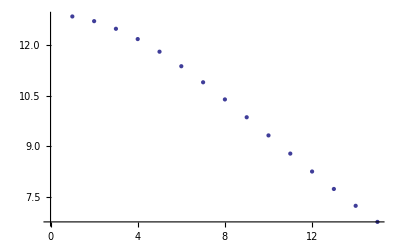

```mathematica
ListPlot[%68]
```

```mathematica
Total[%68]
```

152.645

```mathematica
Manipulate[Plot[x BesselJ[0,x ρ[[i]]]RationSinh[x,h,H]Cosh[x(H-x3[[1]])],{x,0,1000},PlotRange->All],{i,0,100}]
```

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

General::stop: 在本次计算中，Part :: partd 的进一步输出将被抑制.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

Part::partd: 部分指定 x3 ⟦ 1 ⟧ 比对象深度更长.

Part::partd: 部分指定 ρ ⟦ 50. ⟧ 比对象深度更长.

General::stop: 在本次计算中，Part :: partd 的进一步输出将被抑制.

```mathematica
S3=NIntegrate[BesselJ[0,ρ[[1]] x]a6[x,h,H],{x,0,1000}]
```

{0.0452211,0.0905506,0.136097,0.181971,0.228284,0.275148,0.322679,0.370998,0.420225,0.470488,0.521918,0.574652,0.628834,0.684613,0.742148,0.801606,0.863162,0.927003,0.993328,1.06235,1.13429,1.2094,1.28792,1.37015,1.45637,1.54692,1.64214,1.7424,1.84812,1.95973,2.07772,2.2026,2.33496,2.47541,2.62463,2.78336,2.95243,3.13273,3.32524,3.53106,3.75138,3.98753,4.24098,4.51337,4.8065,5.1224,5.46332,5.83177,6.23059,6.66295}

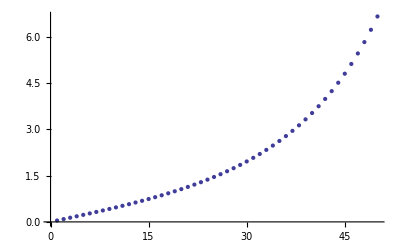

```mathematica
ListPlot[%75]
```

```mathematica
ρ[[1]]
```

1/100

```mathematica
Integrate[BesselJ[2,x],{x,0,Infinity}]
```

1

```mathematica
PrimeQ[1]
```

False

```mathematica
RandomVariate[BesselJZero]
```

RandomVariate::unsdst: 第一个参数 BesselJZero 不是一个有效的分布.

RandomVariate[BesselJZero]

```mathematica
dist=ProbabilityDistribution[x^4/(Sinh[x]^2-(x)^2)/7.266,{x,0,Infinity}]
```

ProbabilityDistribution[(0.137627 x^4)/(-x^2+Sinh[x]^2),{x,0,∞}]

```mathematica
ProbabilityPlot[ProbabilityDistribution[(0.13762730525736305 x^4)/(-x^2+Sinh[x]^2),{x,0,∞}]]
```

$Aborted

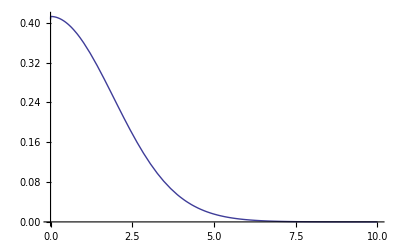

```mathematica
Plot[Evaluate[PDF[dist,x]],{x,0,10},PlotRange->All]
```

```mathematica
NIntegrate[PDF[dist,x],{x,0,Infinity}]
```

1.

Power::infy: 碰到无穷表达式 1/0..

Infinity::indet: 碰到不定表达式 ComplexInfinity + ComplexInfinity.

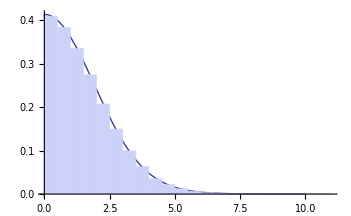

```mathematica
data=RandomVariate[dist,400000];
Show[Plot[Evaluate[PDF[dist,x]],{x,0,10},PlotStyle->Thick,PlotRange->All],
Histogram[data,20,"ProbabilityDensity"]
]
```

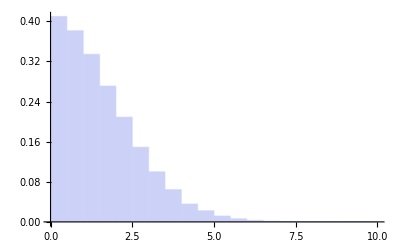

```mathematica
Histogram[data,20,"ProbabilityDensity"]
```

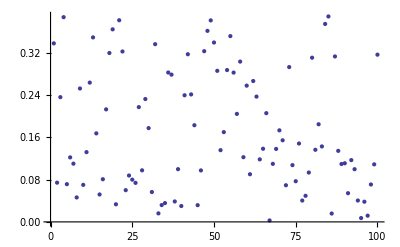

```mathematica
Integrate[x^4/(Sinh[x]^2-(x)^2),{x,0,100}]
```

$Aborted

```mathematica
NIntegrate[x^4/(-x^2+Sinh[x]^2),{x,0,100}]
```

7.266

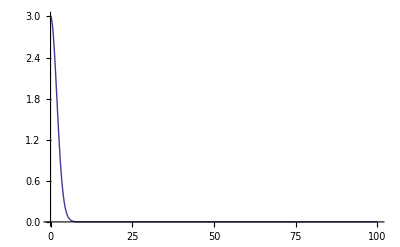

```mathematica
Plot[x^4/(Sinh[x]^2-(x)^2),{x,0,100},PlotRange->All]
```

```mathematica
Limit[x^4/(Sinh[x]^2-x^2),x->0]
```

3

```mathematica
data[[;;10]]
```

{1.35683,1.11351,2.51014,0.902519,2.77529,2.13475,0.590037,4.10009,1.88006,2.22966}

```mathematica
(* 开始 monte carlo 模拟求积分*)
```

```mathematica
n=200000;
sample=RandomVariate[dist,n];
integral=Mean[BesselJ[0,ρ #]a6bar[#,h,H]&/@sample/.{h->0.1,H->1,x3->0.2,ρ->0.1}]
```

-0.548625

40000

```mathematica
sample=RandomVariate[dist,2]
```

{1.04844,0.429837}

```mathematica
BesselJ[0,ρ #]a6bar[#,h,H]&/@sample/.{h->0.1,H->1,x3->0.2,ρ->0.1}
```

{-0.0341351,-0.0109154}

```mathematica
Plot[BesselJ[0,ρ x]a6bar[x,h,H]/.{h->0.1,H->1,x3->0.2,ρ->0.1},{x,0,100},PlotRange->All]
```

-Graphics-

```mathematica
h0=0.1;m=100;H=1;
z=Table[h0+i/m,{i,0,(H-h0)m}];
NIntegrate[BesselJ[0,ρ x]a6[x,h,H]/.{h->h0,H->1,x3->#,ρ->0.1}&/@z,{x,0,200}]
```

{-12.4975,-11.4638,-10.5092,-9.63348,-8.83398,-8.10631,-7.44533,-6.8456,-6.3017,-5.80846,-5.36099,-4.95478,-4.58573,-4.2501,-3.94451,-3.66596,-3.41171,-3.17936,-2.96672,-2.77187,-2.59306,-2.42877,-2.2776,-2.13833,-2.00983,-1.89114,-1.78135,-1.67967,-1.58539,-1.49785,-1.41648,-1.34075,-1.27018,-1.20436,-1.14289,-1.08542,-1.03163,-0.981236,-0.933962,-0.889572,-0.847846,-0.808583,-0.771599,-0.736724,-0.703804,-0.672696,-0.643271,-0.615406,-0.58899,-0.563921,-0.540103,-0.517448,-0.495874,-0.475305,-0.455669,-0.436901,-0.418938,-0.401723,-0.3852,-0.369318,-0.35403,-0.339288,-0.325051,-0.311275,-0.297922,-0.284955,-0.272336,-0.26003,-0.248005,-0.236226,-0.224662,-0.21328,-0.202051,-0.190942,-0.179924,-0.168966,-0.158036,-0.147105,-0.136139,-0.125107,-0.113977,-0.102714,-0.0912828,-0.0796478,-0.0677708,-0.0556123,-0.0431308,-0.0302826,-0.0170216,-0.00329883,0.0109375}

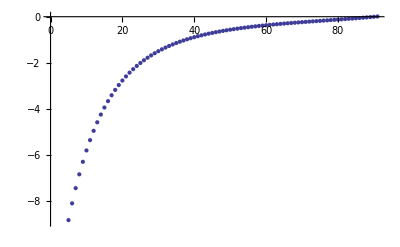

```mathematica
ListPlot[%144]
```

```mathematica
Manipulate[Plot[BesselJ[0,ρ x]a6[x,h,H]/.{h->h0,H->1,x3->xz,ρ->0.1},{x,0,100},PlotRange->All],{xz,z}]
```

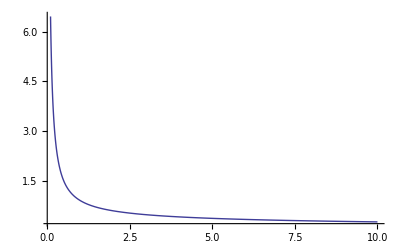

```mathematica
Plot[Abs[HankelH1[1,x]],{x,0.1,10},PlotRange->All]
```

```mathematica
Simplify[HankelH1[1,x]]
```

HankelH1[1,x]

```mathematica
(* 取 k=3. 先令H=1*)
-Graphics-
```

```mathematica
Clear["Global`*"]
H=1;
```

```mathematica
(* x = x3/H, y = h/H, r = ρ/H*)
p[x_,y_,r_]:=1/(2 H^2)Im[Sum[HankelH1[0,z[[m]]*r]/(√(1+z[[m]]^2)-1)*z[[m]]*(Sinh[y z[[m]]]*Cosh[x z[[m]]]
y*z[[m]]*(z[[m]]*Sinh[(x+y)*z[[m]]]-√(1+z[[m]]^2)*Cosh[(x+y)*z[[m]]]-Cosh[(x-y)*z[[m]]])+
Sinh[y*z[[m]]](√(1+z[[m]]^2)*Cos[x*z[[m]]]-z[[m]]*Sinh[x*z[[m]]])),{m,1,6}]]
```

-Graphics3D-

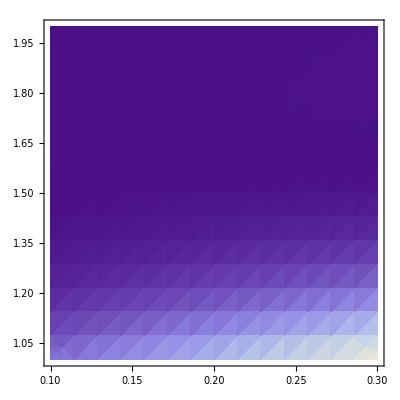

```mathematica
h0=0.1;
Plot3D[Abs[p[x,h0,r]],{x,1h0,3h0},{r,10h0,20h0},PlotRange->All]
DensityPlot[Abs[p[x,h0,r]],{x,1h0,3h0},{r,10h0,20h0},PlotRange->All]
```

```mathematica
NSolve[Sinh[z]^2==z^2,z]
```

NSolve::nsmet: 无法利用 NSolve 现有的方法求解该系统.

```mathematica
FindRoot[Sinh[z]^2==z^2,{z,2}]
```

{z→2.59546×10^-8}

```mathematica
z={2.2507+I 4.2124,2.7687+I 7.4977,3.1031+I 10.7125,
	3.3522+I 13.8999,3.5511+I 17.0734,3.7168+I 20.2385}
```

{2.2507+4.2124 ⅈ,2.7687+7.4977 ⅈ,3.1031+10.7125 ⅈ,3.3522+13.8999 ⅈ,3.5511+17.0734 ⅈ,3.7168+20.2385 ⅈ}

```mathematica
p[x,y,z]
```

{1/2 Im[(-5.94407×10^-10-8.89997×10^-10 ⅈ) (((2.30119+4.11997 ⅈ) Cos[(2.2507+4.2124 ⅈ) x]-(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) x]) Sinh[(2.2507+4.2124 ⅈ) y]+(2.2507+4.2124 ⅈ) y Cosh[(2.2507+4.2124 ⅈ) x] Sinh[(2.2507+4.2124 ⅈ) y] (-Cosh[(2.2507+4.2124 ⅈ) (x-y)]-(2.30119+4.11997 ⅈ) Cosh[(2.2507+4.2124 ⅈ) (x+y)]+(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) (x3+y)]))-(3.49048×10^-14+4.16408×10^-14 ⅈ) (((2.79059+7.4389 ⅈ) Cos[(2.7687+7.4977 ⅈ) x]-(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) x]) Sinh[(2.7687+7.4977 ⅈ) y]+(2.7687+7.4977 ⅈ) y Cosh[(2.7687+7.4977 ⅈ) x] Sinh[(2.7687+7.4977 ⅈ) y] (-Cosh[(2.7687+7.4977 ⅈ) (x-y)]-(2.79059+7.4389 ⅈ) Cosh[(2.7687+7.4977 ⅈ) (x+y)]+(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) (x3+y)]))-(6.35992×10^-18+4.78596×10^-18 ⅈ) (((3.11564+10.6694 ⅈ) Cos[(3.1031+10.7125 ⅈ) x]-(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) x]) Sinh[(3.1031+10.7125 ⅈ) y]+(3.1031+10.7125 ⅈ) y Cosh[(3.1031+10.7125 ⅈ) x] Sinh[(3.1031+10.7125 ⅈ) y] (-Cosh[(3.1031+10.7125 ⅈ) (x-y)]-(3.11564+10.6694 ⅈ) Cosh[(3.1031+10.7125 ⅈ) (x+y)]+(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) (x3+y)]))-(1.76352×10^-21+6.25294×10^-22 ⅈ) (((3.36043+13.8659 ⅈ) Cos[(3.3522+13.8999 ⅈ) x]-(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) x]) Sinh[(3.3522+13.8999 ⅈ) y]+(3.3522+13.8999 ⅈ) y Cosh[(3.3522+13.8999 ⅈ) x] Sinh[(3.3522+13.8999 ⅈ) y] (-Cosh[(3.3522+13.8999 ⅈ) (x-y)]-(3.36043+13.8659 ⅈ) Cosh[(3.3522+13.8999 ⅈ) (x+y)]+(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) (x3+y)]))-(5.76908×10^-25-1.00468×10^-26 ⅈ) (((3.55695+17.0453 ⅈ) Cos[(3.5511+17.0734 ⅈ) x]-(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) x]) Sinh[(3.5511+17.0734 ⅈ) y]+(3.5511+17.0734 ⅈ) y Cosh[(3.5511+17.0734 ⅈ) x] Sinh[(3.5511+17.0734 ⅈ) y] (-Cosh[(3.5511+17.0734 ⅈ) (x-y)]-(3.55695+17.0453 ⅈ) Cosh[(3.5511+17.0734 ⅈ) (x+y)]+(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) (x3+y)]))-(1.94423×10^-28-8.54962×10^-29 ⅈ) (((3.7212+20.2146 ⅈ) Cos[(3.7168+20.2385 ⅈ) x]-(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) x]) Sinh[(3.7168+20.2385 ⅈ) y]+(3.7168+20.2385 ⅈ) y Cosh[(3.7168+20.2385 ⅈ) x] Sinh[(3.7168+20.2385 ⅈ) y] (-Cosh[(3.7168+20.2385 ⅈ) (x-y)]-(3.7212+20.2146 ⅈ) Cosh[(3.7168+20.2385 ⅈ) (x+y)]+(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) (x3+y)]))],1/2 Im[(-3.98154×10^-14-4.14824×10^-14 ⅈ) (((2.30119+4.11997 ⅈ) Cos[(2.2507+4.2124 ⅈ) x]-(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) x]) Sinh[(2.2507+4.2124 ⅈ) y]+(2.2507+4.2124 ⅈ) y Cosh[(2.2507+4.2124 ⅈ) x] Sinh[(2.2507+4.2124 ⅈ) y] (-Cosh[(2.2507+4.2124 ⅈ) (x-y)]-(2.30119+4.11997 ⅈ) Cosh[(2.2507+4.2124 ⅈ) (x+y)]+(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) (x3+y)]))+(8.92233×10^-20-3.80213×10^-20 ⅈ) (((2.79059+7.4389 ⅈ) Cos[(2.7687+7.4977 ⅈ) x]-(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) x]) Sinh[(2.7687+7.4977 ⅈ) y]+(2.7687+7.4977 ⅈ) y Cosh[(2.7687+7.4977 ⅈ) x] Sinh[(2.7687+7.4977 ⅈ) y] (-Cosh[(2.7687+7.4977 ⅈ) (x-y)]-(2.79059+7.4389 ⅈ) Cosh[(2.7687+7.4977 ⅈ) (x+y)]+(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) (x3+y)]))+(2.10937×10^-26+8.95171×10^-25 ⅈ) (((3.11564+10.6694 ⅈ) Cos[(3.1031+10.7125 ⅈ) x]-(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) x]) Sinh[(3.1031+10.7125 ⅈ) y]+(3.1031+10.7125 ⅈ) y Cosh[(3.1031+10.7125 ⅈ) x] Sinh[(3.1031+10.7125 ⅈ) y] (-Cosh[(3.1031+10.7125 ⅈ) (x-y)]-(3.11564+10.6694 ⅈ) Cosh[(3.1031+10.7125 ⅈ) (x+y)]+(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) (x3+y)]))-(1.68774×10^-29+5.69056×10^-30 ⅈ) (((3.36043+13.8659 ⅈ) Cos[(3.3522+13.8999 ⅈ) x]-(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) x]) Sinh[(3.3522+13.8999 ⅈ) y]+(3.3522+13.8999 ⅈ) y Cosh[(3.3522+13.8999 ⅈ) x] Sinh[(3.3522+13.8999 ⅈ) y] (-Cosh[(3.3522+13.8999 ⅈ) (x-y)]-(3.36043+13.8659 ⅈ) Cosh[(3.3522+13.8999 ⅈ) (x+y)]+(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) (x3+y)]))+(3.29614×10^-34-4.42876×10^-34 ⅈ) (((3.55695+17.0453 ⅈ) Cos[(3.5511+17.0734 ⅈ) x]-(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) x]) Sinh[(3.5511+17.0734 ⅈ) y]+(3.5511+17.0734 ⅈ) y Cosh[(3.5511+17.0734 ⅈ) x] Sinh[(3.5511+17.0734 ⅈ) y] (-Cosh[(3.5511+17.0734 ⅈ) (x-y)]-(3.55695+17.0453 ⅈ) Cosh[(3.5511+17.0734 ⅈ) (x+y)]+(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) (x3+y)]))+(1.37505×10^-38+1.82881×10^-38 ⅈ) (((3.7212+20.2146 ⅈ) Cos[(3.7168+20.2385 ⅈ) x]-(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) x]) Sinh[(3.7168+20.2385 ⅈ) y]+(3.7168+20.2385 ⅈ) y Cosh[(3.7168+20.2385 ⅈ) x] Sinh[(3.7168+20.2385 ⅈ) y] (-Cosh[(3.7168+20.2385 ⅈ) (x-y)]-(3.7212+20.2146 ⅈ) Cosh[(3.7168+20.2385 ⅈ) (x+y)]+(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) (x3+y)]))],1/2 Im[(-7.33106×10^-18-4.45962×10^-18 ⅈ) (((2.30119+4.11997 ⅈ) Cos[(2.2507+4.2124 ⅈ) x]-(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) x]) Sinh[(2.2507+4.2124 ⅈ) y]+(2.2507+4.2124 ⅈ) y Cosh[(2.2507+4.2124 ⅈ) x] Sinh[(2.2507+4.2124 ⅈ) y] (-Cosh[(2.2507+4.2124 ⅈ) (x-y)]-(2.30119+4.11997 ⅈ) Cosh[(2.2507+4.2124 ⅈ) (x+y)]+(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) (x3+y)]))+(5.00426×10^-26+9.10848×10^-25 ⅈ) (((2.79059+7.4389 ⅈ) Cos[(2.7687+7.4977 ⅈ) x]-(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) x]) Sinh[(2.7687+7.4977 ⅈ) y]+(2.7687+7.4977 ⅈ) y Cosh[(2.7687+7.4977 ⅈ) x] Sinh[(2.7687+7.4977 ⅈ) y] (-Cosh[(2.7687+7.4977 ⅈ) (x-y)]-(2.79059+7.4389 ⅈ) Cosh[(2.7687+7.4977 ⅈ) (x+y)]+(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) (x3+y)]))+(8.7275×10^-31-4.47589×10^-31 ⅈ) (((3.11564+10.6694 ⅈ) Cos[(3.1031+10.7125 ⅈ) x]-(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) x]) Sinh[(3.1031+10.7125 ⅈ) y]+(3.1031+10.7125 ⅈ) y Cosh[(3.1031+10.7125 ⅈ) x] Sinh[(3.1031+10.7125 ⅈ) y] (-Cosh[(3.1031+10.7125 ⅈ) (x-y)]-(3.11564+10.6694 ⅈ) Cosh[(3.1031+10.7125 ⅈ) (x+y)]+(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) (x3+y)]))-(2.29374×10^-36+1.95943×10^-36 ⅈ) (((3.36043+13.8659 ⅈ) Cos[(3.3522+13.8999 ⅈ) x]-(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) x]) Sinh[(3.3522+13.8999 ⅈ) y]+(3.3522+13.8999 ⅈ) y Cosh[(3.3522+13.8999 ⅈ) x] Sinh[(3.3522+13.8999 ⅈ) y] (-Cosh[(3.3522+13.8999 ⅈ) (x-y)]-(3.36043+13.8659 ⅈ) Cosh[(3.3522+13.8999 ⅈ) (x+y)]+(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) (x3+y)]))-(5.21934×10^-42-1.6253×10^-41 ⅈ) (((3.55695+17.0453 ⅈ) Cos[(3.5511+17.0734 ⅈ) x]-(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) x]) Sinh[(3.5511+17.0734 ⅈ) y]+(3.5511+17.0734 ⅈ) y Cosh[(3.5511+17.0734 ⅈ) x] Sinh[(3.5511+17.0734 ⅈ) y] (-Cosh[(3.5511+17.0734 ⅈ) (x-y)]-(3.55695+17.0453 ⅈ) Cosh[(3.5511+17.0734 ⅈ) (x+y)]+(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) (x3+y)]))+(1.43421×10^-46-1.40928×10^-47 ⅈ) (((3.7212+20.2146 ⅈ) Cos[(3.7168+20.2385 ⅈ) x]-(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) x]) Sinh[(3.7168+20.2385 ⅈ) y]+(3.7168+20.2385 ⅈ) y Cosh[(3.7168+20.2385 ⅈ) x] Sinh[(3.7168+20.2385 ⅈ) y] (-Cosh[(3.7168+20.2385 ⅈ) (x-y)]-(3.7212+20.2146 ⅈ) Cosh[(3.7168+20.2385 ⅈ) (x+y)]+(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) (x3+y)]))],1/2 Im[(-1.98379×10^-21-4.51896×10^-22 ⅈ) (((2.30119+4.11997 ⅈ) Cos[(2.2507+4.2124 ⅈ) x]-(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) x]) Sinh[(2.2507+4.2124 ⅈ) y]+(2.2507+4.2124 ⅈ) y Cosh[(2.2507+4.2124 ⅈ) x] Sinh[(2.2507+4.2124 ⅈ) y] (-Cosh[(2.2507+4.2124 ⅈ) (x-y)]-(2.30119+4.11997 ⅈ) Cosh[(2.2507+4.2124 ⅈ) (x+y)]+(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) (x3+y)]))-(1.76107×10^-29+4.98223×10^-30 ⅈ) (((2.79059+7.4389 ⅈ) Cos[(2.7687+7.4977 ⅈ) x]-(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) x]) Sinh[(2.7687+7.4977 ⅈ) y]+(2.7687+7.4977 ⅈ) y Cosh[(2.7687+7.4977 ⅈ) x] Sinh[(2.7687+7.4977 ⅈ) y] (-Cosh[(2.7687+7.4977 ⅈ) (x-y)]-(2.79059+7.4389 ⅈ) Cosh[(2.7687+7.4977 ⅈ) (x+y)]+(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) (x3+y)]))-(2.34909×10^-36+1.934×10^-36 ⅈ) (((3.11564+10.6694 ⅈ) Cos[(3.1031+10.7125 ⅈ) x]-(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) x]) Sinh[(3.1031+10.7125 ⅈ) y]+(3.1031+10.7125 ⅈ) y Cosh[(3.1031+10.7125 ⅈ) x] Sinh[(3.1031+10.7125 ⅈ) y] (-Cosh[(3.1031+10.7125 ⅈ) (x-y)]-(3.11564+10.6694 ⅈ) Cosh[(3.1031+10.7125 ⅈ) (x+y)]+(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) (x3+y)]))-(6.98353×10^-43+1.78021×10^-42 ⅈ) (((3.36043+13.8659 ⅈ) Cos[(3.3522+13.8999 ⅈ) x]-(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) x]) Sinh[(3.3522+13.8999 ⅈ) y]+(3.3522+13.8999 ⅈ) y Cosh[(3.3522+13.8999 ⅈ) x] Sinh[(3.3522+13.8999 ⅈ) y] (-Cosh[(3.3522+13.8999 ⅈ) (x-y)]-(3.36043+13.8659 ⅈ) Cosh[(3.3522+13.8999 ⅈ) (x+y)]+(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) (x3+y)]))+(4.14469×10^-49-2.57058×10^-48 ⅈ) (((3.55695+17.0453 ⅈ) Cos[(3.5511+17.0734 ⅈ) x]-(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) x]) Sinh[(3.5511+17.0734 ⅈ) y]+(3.5511+17.0734 ⅈ) y Cosh[(3.5511+17.0734 ⅈ) x] Sinh[(3.5511+17.0734 ⅈ) y] (-Cosh[(3.5511+17.0734 ⅈ) (x-y)]-(3.55695+17.0453 ⅈ) Cosh[(3.5511+17.0734 ⅈ) (x+y)]+(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) (x3+y)]))+(3.79403×10^-54-4.508×10^-54 ⅈ) (((3.7212+20.2146 ⅈ) Cos[(3.7168+20.2385 ⅈ) x]-(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) x]) Sinh[(3.7168+20.2385 ⅈ) y]+(3.7168+20.2385 ⅈ) y Cosh[(3.7168+20.2385 ⅈ) x] Sinh[(3.7168+20.2385 ⅈ) y] (-Cosh[(3.7168+20.2385 ⅈ) (x-y)]-(3.7212+20.2146 ⅈ) Cosh[(3.7168+20.2385 ⅈ) (x+y)]+(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) (x3+y)]))],1/2 Im[(-6.23688×10^-25+9.17402×10^-26 ⅈ) (((2.30119+4.11997 ⅈ) Cos[(2.2507+4.2124 ⅈ) x]-(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) x]) Sinh[(2.2507+4.2124 ⅈ) y]+(2.2507+4.2124 ⅈ) y Cosh[(2.2507+4.2124 ⅈ) x] Sinh[(2.2507+4.2124 ⅈ) y] (-Cosh[(2.2507+4.2124 ⅈ) (x-y)]-(2.30119+4.11997 ⅈ) Cosh[(2.2507+4.2124 ⅈ) (x+y)]+(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) (x3+y)]))+(3.1163×10^-34-4.77255×10^-34 ⅈ) (((2.79059+7.4389 ⅈ) Cos[(2.7687+7.4977 ⅈ) x]-(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) x]) Sinh[(2.7687+7.4977 ⅈ) y]+(2.7687+7.4977 ⅈ) y Cosh[(2.7687+7.4977 ⅈ) x] Sinh[(2.7687+7.4977 ⅈ) y] (-Cosh[(2.7687+7.4977 ⅈ) (x-y)]-(2.79059+7.4389 ⅈ) Cosh[(2.7687+7.4977 ⅈ) (x+y)]+(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) (x3+y)]))-(4.79242×10^-42-1.66227×10^-41 ⅈ) (((3.11564+10.6694 ⅈ) Cos[(3.1031+10.7125 ⅈ) x]-(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) x]) Sinh[(3.1031+10.7125 ⅈ) y]+(3.1031+10.7125 ⅈ) y Cosh[(3.1031+10.7125 ⅈ) x] Sinh[(3.1031+10.7125 ⅈ) y] (-Cosh[(3.1031+10.7125 ⅈ) (x-y)]-(3.11564+10.6694 ⅈ) Cosh[(3.1031+10.7125 ⅈ) (x+y)]+(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) (x3+y)]))+(3.85767×10^-49-2.58755×10^-48 ⅈ) (((3.36043+13.8659 ⅈ) Cos[(3.3522+13.8999 ⅈ) x]-(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) x]) Sinh[(3.3522+13.8999 ⅈ) y]+(3.3522+13.8999 ⅈ) y Cosh[(3.3522+13.8999 ⅈ) x] Sinh[(3.3522+13.8999 ⅈ) y] (-Cosh[(3.3522+13.8999 ⅈ) (x-y)]-(3.36043+13.8659 ⅈ) Cosh[(3.3522+13.8999 ⅈ) (x+y)]+(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) (x3+y)]))-(7.54734×10^-56-1.00514×10^-54 ⅈ) (((3.55695+17.0453 ⅈ) Cos[(3.5511+17.0734 ⅈ) x]-(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) x]) Sinh[(3.5511+17.0734 ⅈ) y]+(3.5511+17.0734 ⅈ) y Cosh[(3.5511+17.0734 ⅈ) x] Sinh[(3.5511+17.0734 ⅈ) y] (-Cosh[(3.5511+17.0734 ⅈ) (x-y)]-(3.55695+17.0453 ⅈ) Cosh[(3.5511+17.0734 ⅈ) (x+y)]+(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) (x3+y)]))+(2.01103×10^-62-7.18057×10^-61 ⅈ) (((3.7212+20.2146 ⅈ) Cos[(3.7168+20.2385 ⅈ) x]-(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) x]) Sinh[(3.7168+20.2385 ⅈ) y]+(3.7168+20.2385 ⅈ) y Cosh[(3.7168+20.2385 ⅈ) x] Sinh[(3.7168+20.2385 ⅈ) y] (-Cosh[(3.7168+20.2385 ⅈ) (x-y)]-(3.7212+20.2146 ⅈ) Cosh[(3.7168+20.2385 ⅈ) (x+y)]+(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) (x3+y)]))],1/2 Im[(-1.98248×10^-28+1.21895×10^-28 ⅈ) (((2.30119+4.11997 ⅈ) Cos[(2.2507+4.2124 ⅈ) x]-(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) x]) Sinh[(2.2507+4.2124 ⅈ) y]+(2.2507+4.2124 ⅈ) y Cosh[(2.2507+4.2124 ⅈ) x] Sinh[(2.2507+4.2124 ⅈ) y] (-Cosh[(2.2507+4.2124 ⅈ) (x-y)]-(2.30119+4.11997 ⅈ) Cosh[(2.2507+4.2124 ⅈ) (x+y)]+(2.2507+4.2124 ⅈ) Sinh[(2.2507+4.2124 ⅈ) (x3+y)]))+(1.55225×10^-38+1.78987×10^-38 ⅈ) (((2.79059+7.4389 ⅈ) Cos[(2.7687+7.4977 ⅈ) x]-(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) x]) Sinh[(2.7687+7.4977 ⅈ) y]+(2.7687+7.4977 ⅈ) y Cosh[(2.7687+7.4977 ⅈ) x] Sinh[(2.7687+7.4977 ⅈ) y] (-Cosh[(2.7687+7.4977 ⅈ) (x-y)]-(2.79059+7.4389 ⅈ) Cosh[(2.7687+7.4977 ⅈ) (x+y)]+(2.7687+7.4977 ⅈ) Sinh[(2.7687+7.4977 ⅈ) (x3+y)]))+(1.45114×10^-46-1.99075×10^-47 ⅈ) (((3.11564+10.6694 ⅈ) Cos[(3.1031+10.7125 ⅈ) x]-(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) x]) Sinh[(3.1031+10.7125 ⅈ) y]+(3.1031+10.7125 ⅈ) y Cosh[(3.1031+10.7125 ⅈ) x] Sinh[(3.1031+10.7125 ⅈ) y] (-Cosh[(3.1031+10.7125 ⅈ) (x-y)]-(3.11564+10.6694 ⅈ) Cosh[(3.1031+10.7125 ⅈ) (x+y)]+(3.1031+10.7125 ⅈ) Sinh[(3.1031+10.7125 ⅈ) (x3+y)]))+(3.73054×10^-54-4.61895×10^-54 ⅈ) (((3.36043+13.8659 ⅈ) Cos[(3.3522+13.8999 ⅈ) x]-(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) x]) Sinh[(3.3522+13.8999 ⅈ) y]+(3.3522+13.8999 ⅈ) y Cosh[(3.3522+13.8999 ⅈ) x] Sinh[(3.3522+13.8999 ⅈ) y] (-Cosh[(3.3522+13.8999 ⅈ) (x-y)]-(3.36043+13.8659 ⅈ) Cosh[(3.3522+13.8999 ⅈ) (x+y)]+(3.3522+13.8999 ⅈ) Sinh[(3.3522+13.8999 ⅈ) (x3+y)]))+(1.41531×10^-62-7.20291×10^-61 ⅈ) (((3.55695+17.0453 ⅈ) Cos[(3.5511+17.0734 ⅈ) x]-(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) x]) Sinh[(3.5511+17.0734 ⅈ) y]+(3.5511+17.0734 ⅈ) y Cosh[(3.5511+17.0734 ⅈ) x] Sinh[(3.5511+17.0734 ⅈ) y] (-Cosh[(3.5511+17.0734 ⅈ) (x-y)]-(3.55695+17.0453 ⅈ) Cosh[(3.5511+17.0734 ⅈ) (x+y)]+(3.5511+17.0734 ⅈ) Sinh[(3.5511+17.0734 ⅈ) (x3+y)]))-(1.00502×10^-67+1.4916×10^-67 ⅈ) (((3.7212+20.2146 ⅈ) Cos[(3.7168+20.2385 ⅈ) x]-(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) x]) Sinh[(3.7168+20.2385 ⅈ) y]+(3.7168+20.2385 ⅈ) y Cosh[(3.7168+20.2385 ⅈ) x] Sinh[(3.7168+20.2385 ⅈ) y] (-Cosh[(3.7168+20.2385 ⅈ) (x-y)]-(3.7212+20.2146 ⅈ) Cosh[(3.7168+20.2385 ⅈ) (x+y)]+(3.7168+20.2385 ⅈ) Sinh[(3.7168+20.2385 ⅈ) (x3+y)]))]}

```mathematica
z[[1]]
```

2.2507+4.2124 ⅈ

```mathematica
Reduce[Abs[Sinh[x+ⅈ y]^2-(x+ⅈ y)^2]==0,{x,y},Complexes]
```

$Aborted

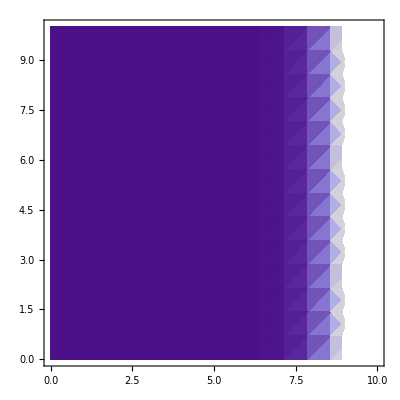

```mathematica
DensityPlot[{Abs[Sinh[x+ⅈ y]^2-(x+ⅈ y)^2]},{x,0,10},{y,0,10}]
```

```mathematica
(Sinh[z[[2]]])^2-z[[2]]^2
```

-0.00382136-0.000933415 ⅈ

```mathematica
Table[Log [2m+1]Pi+ⅈ (m+0.5)Pi,{m,1,7}]
```

{3.45139+4.71239 ⅈ,5.0562+7.85398 ⅈ,6.11326+10.9956 ⅈ,6.90278+14.1372 ⅈ,7.53321+17.2788 ⅈ,8.05803+20.4204 ⅈ,8.50759+23.5619 ⅈ}

```mathematica
FindRoot[Sinh[x]^2-(x)^2==0,{x,33.451392295223203+4.71238898038469 ⅈ}]
```

{x→2.25073+4.21239 ⅈ}

```mathematica
a1[x_,h_,H_]:=1/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*x3*Sinh[x*(H-x3)]Sinh[x(H-h)]
+x3(h Sinh[x H]Cosh[x(H-x3-h)])-H Sinh[x*h]Cosh[x3 H])
+x3 x H Sinh[x H]Cosh[x(H-x3)]raSinh[x,H-h,H]
-H Sinh[x x3](Sinh[x*H] raSinh[x,h,H]+x*H raSinh[x,H-h,H])
);

a2[x_,h_,H_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
x3((H Sinh[x*H]Cosh[x x3]-h Sinh[x H]Cosh[x(H-x3-h)]
+x h H Sinh[x*(H-x3)]Sinh[x (H-h)])
+x H Cosh[x(H-x3)]Sinh[x*H] raSinh[x,H-h,H]
-x*H^2 Sinh[x x3] raSinh[x,H-h,H])+H Sinh[x*x3]*Sinh[x*H] raSinh[x,h,H]
);

a3[x_,h_,H_]:=(Sinh[x*H]^2)^-1*
(h*Sinh[x*H]Cosh[x(H-x3-h)]-H*Sinh[x*h]Cosh[x(H+x3)]);

a4[x_,h_,H_]:=x/(Sinh[x*H]^2-(x*H)^2)*(
x3 x H(h Sinh[x (x3-h)]
+H Sinh[x h]Sinh[x(H-x3)]/Sinh[x H]
-x h H^2 Sinh[x x3]Sinh[x(H-h)]/Sinh[x H]
+(KroneckerDelta[j,3]-KroneckerDelta[k,3])
*(-H(H-h)Sinh[x h]Sinh[x x3]+x3(h Sinh[x H]Sinh[x(H-x3-h)]+H Sinh[x h]Sinh[x x3])))
);

a5[x_,h_,H_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*Sinh[x*(H-h)]+(H-h)Sinh[x*h]Sinh[x H])Cosh[x(H-x3)]+
(Sinh[x*H] raSinh[x,h,H]+x*H raSinh[x,H-h,H])*Sinh[x*H]*Sinh[x*(H-x3)]
);

a6[x_,h_,H_]:=x^2/(Sinh[x*H]^2-(x*H)^2)*(
(x*h*H*Sinh[x*(H-h)]-(H-h)Sinh[x*h]Sinh[x H])Sinh[x(H-x3)]-
(Sinh[x*H] raSinh[x,h,H]-x*H raSinh[x,H-h,H])*Sinh[x*H]*Cosh[x*(H-x3)]
);
```

```mathematica
h=0.1;
```

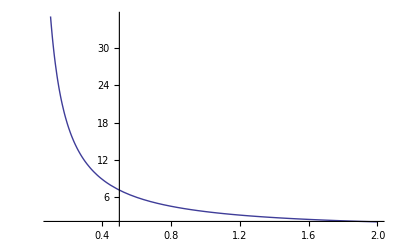

```mathematica
Plot[BesselJ[0,√2 h x]a2[x,h,10h]/.x3->2.5h,{x,0.1,2},PlotRange->All]
```